```mathematica
Tair = 750; Trod = 750; Tinit = 298;
r1 = 5/1000; r2 = 1.8/100; r3 = 2/100;
h = 50; ϵ = 0.95; σ = 5.67*10^-7;
k = 0.01;cpBase = 2000; ρ = 0.5;  
Hburn = 5645000/.3423 ;(*J/kg*)
Hmelt = 2221000/.3423 ;(*J/mg*)
```

```mathematica
gauss[temp_, mean_, std_]:= PDF[ NormalDistribution[mean,std],temp]
cpInterior[temp_]:= cpBase+Hmelt*gauss[temp,186+273,0.4 ] 
cpExterior[temp_]:= cpBase+Hburn*gauss[temp,186+273,0.4 ] 
cp[rSquared_, temp_]:= Piecewise[{{cpInterior[temp], r1^2<=rSquared<r2^2}, {cpExterior[temp], rSquared >= r2^2}}]
```

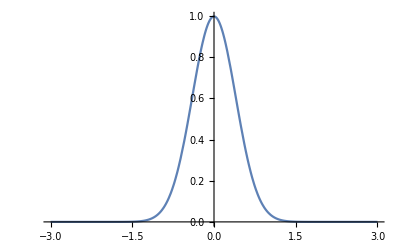

1.

```mathematica
Plot[gauss[temp, 0, 0.4],{temp,-3,3}, PlotRange->All]
Integrate[gauss[temp, 0, 0.4],{temp,-3,3}]
```

```mathematica
Needs["NDSolve`FEM`"]
```

ElementMesh[{{-0.02,0.02},{-0.02,0.02}},{TriangleElement[<1846>]}]

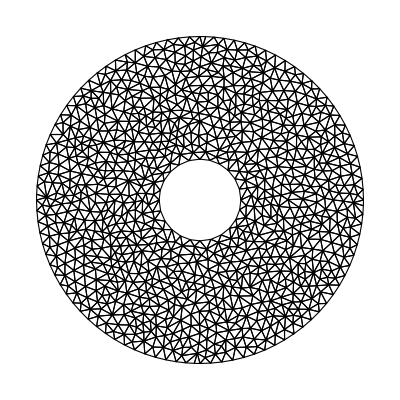

```mathematica
marshmallow = RegionDifference[Disk[{0,0}, r3], Disk[{0,0}, r1]];
mesh = ToElementMesh[marshmallow, "MaxCellMeasure"-> 10^-6, "MeshOrder"->1]
mesh["Wireframe"]
```

```mathematica
pde = HeatTransferPDEComponent[{T[t,x,y], t, {x,y}},
<|"MassDensity" -> ρ, "ThermalConductivity"-> k*IdentityMatrix[2], 
"SpecificHeatCapacity" -> cpBase(*OR USE "cp[x^2+y^2, T[t,x,y]]" TO INCLUDE PHASE CHANGE -- MUCH LONGER RUNTIME!*)
|>
]
```

({{-0.01,0.},{0.,-0.01}}.T[t,x,y]{x,y}Inactive){x,y}Inactive+1000. T^(1,0,0)[t,x,y]

```mathematica
bcInit = T[0,x,y] == Tinit
bcRodFixed = DirichletCondition[T[t,x,y]== Trod, ElementMarker==2]
bcAirConv= NeumannValue[h(Tair-T[t,x,y]), ElementMarker==1]
(*bcAirConvRad = NeumannValue[h(Tair-T[t,x,y])+ ϵ σ (Tair^4-T[t,x,y]^4), ElementMarker==1] 
-> RUNTIME TOO LONG--DID NOT FINISH *)
```

T[0,x,y]==298

DirichletCondition[T[t,x,y]==750,ElementMarker==2]

NeumannValue[50 (750-T[t,x,y]),ElementMarker==1]

```mathematica
simulationTime = 30;
marshmallowHeat = NDSolveValue[{bcInit, bcRodFixed, pde==bcAirConv}, T,{t,0,simulationTime}, {x,y} ∈ mesh]
```

InterpolatingFunction[{{0., 30.}, {-0.02, 0.02}, {-0.02, 0.02}}, <>]

```mathematica
colorTempsCelsius = ColorData["TemperatureMap"][Rescale[#,{Tinit-273,Tair-273}]]&
Manipulate[
Show[
DensityPlot[marshmallowHeat[time,x,y]-273,{x,-r3,r3}, {y, -r3, r3},
 ColorFunctionScaling -> False, ColorFunction-> colorTempsCelsius,
PlotLegends -> BarLegend[{colorTempsCelsius, {Tinit-273, Tair-273}}, LegendLabel->"T [deg C]"],
PlotLabel->Style[StringForm["Marshmallow Temperature \nat t = `` seconds",time],Large]
],
Graphics[{Disk[{0,0},r1], Circle[{0,0},r3]} (*, Dashed, Circle[{0,0},r2],}*)
]
],
{{time, 0, "Time [s]"},0,simulationTime,0.1}]
```

ColorData[TemperatureMap][Rescale[#1,{Tinit-273,Tair-273}]]&

```mathematica
SetDirectory[NotebookDirectory[]]
marshSim2 = ReleaseHold[Import["sim_marsh_2\\export.mx"]]
```

C:\Users\Samuel\Documents\MIT\YEAR-3\semester_6\3.044\3.044_final_proj\3.044_final_code

InterpolatingFunction[{{0., 30.}, {-0.02, 0.02}, {-0.02, 0.02}}, <>]

```mathematica
Manipulate[
Show[
DensityPlot[marshSim2[time,x,y]-273,{x,-r3,r3}, {y, -r3, r3},
 ColorFunctionScaling -> False, ColorFunction-> colorTempsCelsius,
PlotLegends -> BarLegend[{colorTempsCelsius, {Tinit-273, Tair-273}}, LegendLabel->"T [deg C]"],
PlotLabel->Style[StringForm["Marshmallow Temp (with Melting)\nat t = `` seconds",time],Large]
],
Graphics[{Disk[{0,0},r1],Circle[{0,0},r3], Dashed, Circle[{0,0},r2],}]
],
{{time, 0, "Time [s]"},0,30,0.1}]
```